6.48333

22.9333

87.14

6.46667

22.95

87.08

6.46667

22.9667

88.36

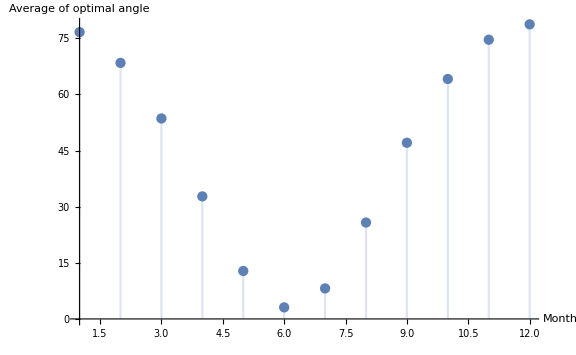
{436.538,-Graphics-}

```mathematica
year = 2016;

powerLoss:= Function[ (* params: hour of day TIMES HUNDRED, solar panel angle, date, returns power loss percentage with this misalignment *)
sunPos = SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[#3,{#1/100}]];
(* remove degree unit, then convert to radians *)
Subscript[γ, s]= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
Subscript[γ, s] = Subscript[γ, s] - Pi;
Subscript[θ, s]= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
Subscript[γ, p] = 0 * Pi/180; (* Solar panels azimuth *)
Subscript[θ, p] = #2 * Pi/180; (* Solar panels angle with horizontal *)
a= ArcCos[Cos[Subscript[γ, p]-Subscript[γ, s]] Cos[Subscript[θ, s]] Sin[Subscript[θ, p]]+Cos[Subscript[θ, p]] Sin[Subscript[θ, s]]];
 1-Cos[a](* 1-Cos[i] gives power loss due to misalignment *)
]

(* Define a function that sums up the total % of power loss at each hour *)
sumPowerLoss:=Function[ (* params: solar panel angle, date *)
position = GeoPosition[{51.546545,4.411744}];
sunUp = Sunrise[position,#2];
sunUpHour = DateValue[sunUp,"Hour"]+DateValue[sunUp, "Minute"]/60;
sunset = Sunset[position,#2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* Times 100 so the sum starts closer to the real sunUpHour, and not floors it to an integer when calculating the sum. Otherwise weird jumps in graphs appear when the sunUpHour jumps one hour *)
 Sum[powerLoss[h,#1,#2],{h,sunUpHour*100,sunsetHour*100,10}] 
]

day := Function[ (* params: day of month, month, returns optimal angle for this day *)
date = DateObject[{2016,#2,#1}];
(* Find for which angle of the solar panels this value is minimal,starting at 50 *)
x /. FindMinimum[sumPowerLoss[x,date],{x,50,0,90}, AccuracyGoal->5][[2]]
]
(* Find value for a specific month by taking the average *)
month := Function [ (* params: month *)
(* Count how many days are in this month *)
days = With[{first=DateObject[{2016,#1,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]] ;
Sum[day[x,#1],{x,1,days}]/days
]

(* ******************* END OF FUNCTIONS ******************************* *)
position = GeoPosition[{51.546545,4.411744}];
sunUp = Sunrise[position,DateObject[{2016,6,5}]];
sunUpHour = DateValue[sunUp,"Hour"]+DateValue[sunUp, "Minute"]/60;
N[sunUpHour]
sunset = Sunset[position,DateObject[{2016,6,5}]];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
N[sunsetHour]
Sum[powerLoss[h,30,DateObject[{2016,6,5}]],{h,sunUpHour*100,sunsetHour*100,10}]
 
sunUp = Sunrise[position,DateObject[{2016,6,6}]];
sunUpHour = DateValue[sunUp,"Hour"]+DateValue[sunUp, "Minute"]/60;
N[sunUpHour]
sunset = Sunset[position,DateObject[{2016,6,6}]];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
N[sunsetHour]
Sum[powerLoss[h,30,DateObject[{2016,6,6}]],{h,sunUpHour*100,sunsetHour*100,10}] 

sunUp = Sunrise[position,DateObject[{2016,6,7}]];
sunUpHour = DateValue[sunUp,"Hour"]+DateValue[sunUp, "Minute"]/60;
N[sunUpHour]
sunset = Sunset[position,DateObject[{2016,6,7}]];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
N[sunsetHour]
Sum[powerLoss[h,30,DateObject[{2016,6,7}]],{h,sunUpHour*100,sunsetHour*100,10}] 
(* DiscretePlot[powerLoss[1430,30,DateObject[{2016,6,d}]],{d,1,30}] *)
(* DiscretePlot[powerLoss[h,30,DateObject[{2016,6,5}]],{h,600,2200,100}]
DiscretePlot[powerLoss[h,30,DateObject[{2016,6,6}]],{h,600,2200,100}]
DiscretePlot[powerLoss[h,30,DateObject[{2016,6,7}]],{h,600,2200,100}]
sumPowerLoss[30,DateObject[{2016,6,5}]]
sumPowerLoss[30,DateObject[{2016,6,6}]]
sumPowerLoss[30,DateObject[{2016,6,7}]]
sumPowerLoss[30,DateObject[{2016,6,8}]] *)



(* Graph for a day *)
(* date = DateObject[{2016,6,20}];
 AbsoluteTiming[DiscretePlot[sumPowerLoss[x,date],{x,0,90,10},ImageSize->Large,AxesLabel -> {"Solar panel angle", "Total of sun power, W/m^2"}] ] *)

(* Graph for a month *)
(*  m = 6;
days = With[{first=DateObject[{year,m,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
AbsoluteTiming[DiscretePlot[day[a,m],{a,1,days},ImageSize->Large,AxesLabel -> {"Day", "Optimal angle"}]] *)

(* Graph for this year *)
 AbsoluteTiming[DiscretePlot[month[x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}] ]
```

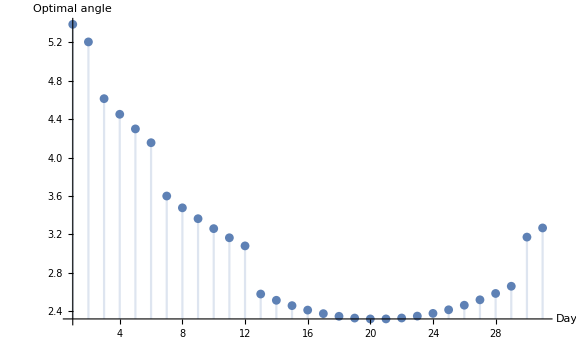
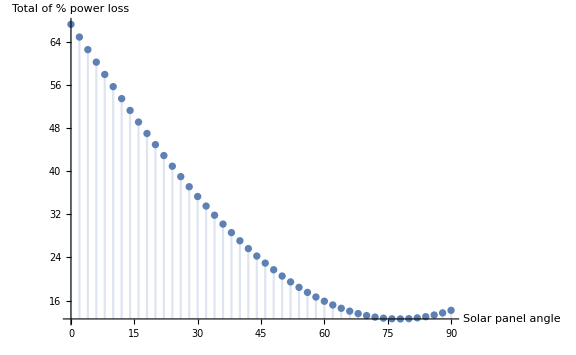
```mathematica
2016: -Graphics-
18/7 
June:-Graphics-
December first:-Graphics-
December:
```